## DivideEdge-Example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (9-Nov-2012)) loaded Fri 9 Nov 2012 05:35:14
using xCellerator 0.90 and XSSA 1204002

```mathematica
w=TemplateRandomSquareGrid[9, {0,0}, {10,10}];
```

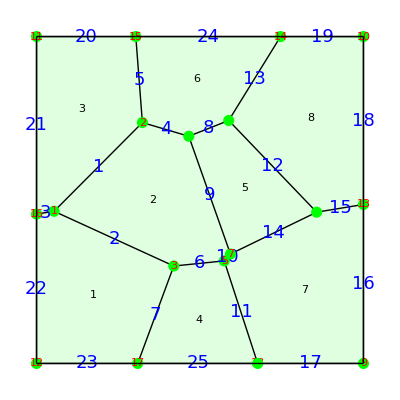

```mathematica
ShowTissue[w,  "Vertices"-> {Green,PointSize[.02]},"VertexNumbers"-> {Red, FontSize-> 18}, "EdgeNumbers"->True, "EdgeNumberStyle"->  {Blue, FontSize-> 18, FontFamily-> "Arial"}, "CellNumbers"-> True]
```

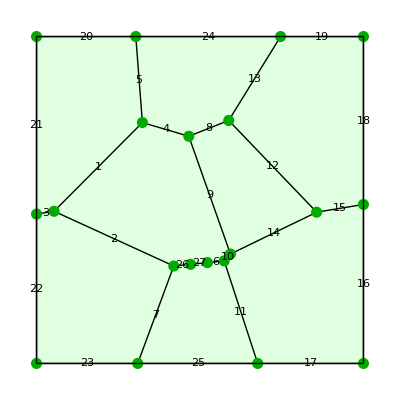

```mathematica
w1=DivideEdge[w, 6, 3];
ShowTissue[w1, "Vertices"-> {Darker[Green], PointSize[.02]}, "EdgeNumbers"-> True]
```

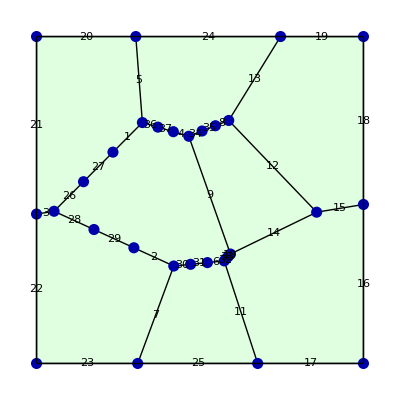

```mathematica
w2=DivideEdges[w, {1,2,6,10,8,4}, 3]; 
ShowTissue[w2, "Vertices"-> {Darker[Blue], PointSize[.02]}, "EdgeNumbers"-> True]
```